{{x→Function[{t},ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]-(e^(ⅈ t) (Cos[(√3 t)/2]^2+Sin[(√3 t)/2]^2))/(-1-ⅈ Log[e]+Log[e]^2)]}}

Function[{t},ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]-(e^(ⅈ t) (Cos[(√3 t)/2]^2+Sin[(√3 t)/2]^2))/(-1-ⅈ Log[e]+Log[e]^2)]

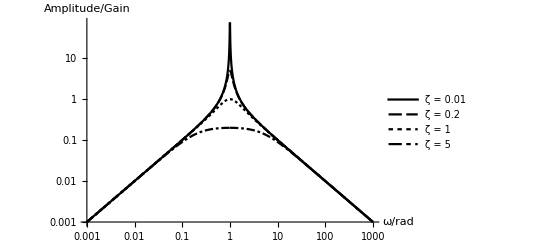

~/Desktop/transfer.png

```mathematica
s= I*ω;
f[ω_,ζ_]:=s/(s^2+ζ*s+1);
sol = DSolve[x''[t]+x'[t]+x[t] == e^(I*Subscript[ω, 0]*t),x,t]
x/.sol[[1]]

p = LogLogPlot[{Abs[f[ω,0.01]],Abs[f[ω,0.2]],Abs[f[ω,1]],Abs[f[ω,5]]},{ω,0.001,1000},PlotRange->All,PlotTheme->"Monochrome" ,AxesLabel->{"ω/rad","Amplitude/Gain"},PlotLegends->{"ζ = 0.01","ζ = 0.2","ζ = 1","ζ = 5"}]
Export["~/Desktop/transfer.png",p]
Clear["Global`*"]
```